# Correlation matrices

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","sp500v2.wdx"}];
database = Import[path];
```

```mathematica
database = SortBy[database,#["Sector"]&];
```

## Correlation matrix

```mathematica
pricesList = Map[Take[#["Prices"],200]&,database];
```

```mathematica
RowCorrelation[rowN_,dataset_]:=Map[Correlation[Part[dataset,rowN],#]&,dataset];
CorrelationMatrix[vectorList_]:=Table[RowCorrelation[i,vectorList],{i,1,Length[vectorList]}];
```

```mathematica
m = CorrelationMatrix[pricesList];
```

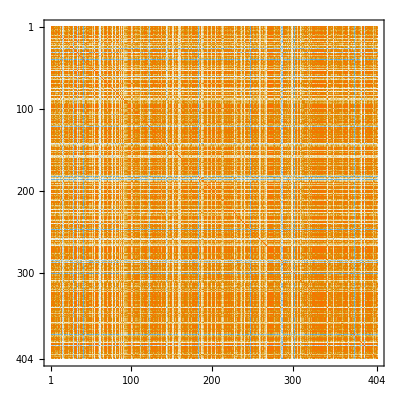

```mathematica
MatrixPlot[m]
```